# Notes on "Quantification of Histochemical Staining by Color Deconvolution"

This is a walkthrough of the color deconvolution method presented in "Quantification of Histochemical Staining by Color Deconvolution", by Arnout C. Ruifrok and Dennis A. Johnston, published in Analytical and Quantitative Cytology and Histology, vol. 23, no. 4, pp. 291-299, August 2001.

When the paper is unclear or ambiguous, reference is made to an ImageJ plugin, Colour_Deconvolution.java. ImageJ is an open source image manipulation and analysis program available at http://rsbweb.nih.gov/ij/.

### Outline of the Method

The method constructs an "OD Matrix" representing the weights of each image color channel (RGB in the paper) for each dye of interest in an image. Each dye is represented by a row in the matrix. Each column represents the weights of a particular color channel. There does not appear to be a fundamental limitation restricting the matrix to three dyes or three color channels. For example, it appears that the rows of RGB weights for each dye could be replaced with multispectral weights.

The paper discusses deconvolution of slides stained with hematoxylin, eosin, and DAB, but does not go into how to handle cases where there are fewer dyes than color channels, an H&E stain for example. The plugin provides a method for handling such cases.

The OD Matrix is manipulated in such a way as to allow an orthonormal transformation of the image data to yield independent information about each dye's contribution to the total stain.

### An RGB Image

Open and retrieve an RGB image for use later in the computations.

```mathematica
imgPath = "~/projects/Color-Deconvolution/Images/3356_001_11889L_9990T.jpg";
img = Import[imgPath]
```

-Graphics-

```mathematica
Dimensions[ImageData[img]]
```

{100,100,3}

#### About this Image

This is a small portion of SI Serialized Slide Number 2861, ScanScope slide number 3356. It is a 100x100 pixel sub-image located at 11,889 pixels from the left and 9,990 pixels from the top of the original, complete image. It is interesting because it has white space to be thresholded and red cells to trick the algorithm. The red cells do not saturate the red channel as they do in some images. An image from a nearby region without red cells is available in 3356_003_11859L_10084T.jpg.

### Options to Control Computation

These are just some global settings that can be used to control how computations are carried out. They are defined here to assure that they are in scope when functions are defined and evaluated later in the document.

```mathematica
options[verbose] = True;
```

The verbose flag controls the level and detail of debugging/tracing messages. Setting the option to False disables most debugging output. Setting it to "veryVerbose" will produce some very detailed output for some functions.

### Convert RGB to OD

The transformation from RGB to OD is conceptually simple. First, the definition of transmittance.

T=I_out/I_inp

where I_out/I_inp is the fraction of the input intensity that makes it through the sample. It is often expressed as a percentage ranging from 0 to 100%. In the case of a scanned image, I_inp is usually related to the resolution of the A/D converter. For an 8-bit camera, the maximum value is 255. However, many scanners, such as the Aperio, calibrate themselves with a smaller value to detect over-saturation. Aperio uses a value of 240, but for simplicity, the description in this explanation will use a value of 255.

The transformation from transmittance to absorbance is almost as straightforward.

OD=-Log10[T]

and ranges in value from 0 (perfectly transparent) to infinity (perfectly opaque.) For numerical analysis reasons, values of 0 are usually replaced with a small number, perhaps the machine precision. Likewise at the other end of the scale, instrumentation is typically unreliable at absorbance values of 3 or greater, so the value of 3 can be used instead of infinity.

Taking a logarithm of every pixel value in an image might be very time consuming, particularly on images of an interesting size. With only 255 possible values, a lookup table might be a faster approach in production code.

```mathematica
(* Convert the data in an image to a matrix of RGB tuples. This function removes the row/column structure from the image data.
Input: img -- an image file. Assumed to be an RGB image.
Output: an array of RGB tuples with byte data elements.*)
convertToRgbTuples[img_]:= Flatten[ImageData[img, "Byte"], 1];
```

```mathematica
Short[convertToRgbTuples[img], 3]
```

{{219,131,169},{209,119,157},{217,118,162},{226,127,171},{222,129,174},{213,128,170},«9989»,{134,109,151},{164,127,168},{174,136,175},{184,146,183},{185,149,185}}

```mathematica
ListPointPlot3D[convertToRgbTuples[img], ColorFunction->Function[{r,g,b},RGBColor[r,g,b]],AxesLabel -> {"R","G","B"}]
```

-Graphics3D-

The "cloud" of pixels off of the main group at high values of R and low values of G is probably due to red cells.

```mathematica
(* Convert a short integer (8-bit byte) in the range of 0 to 255 to absorbance. Assumes that a value of 0 represents 0% transmittance and that 255 represents 100% transmittance. Handles special cases of 0% and 100% transmittance for numerical stability. Forces the result to a numerical value (as opposed to symbolic) using default machine precision. *)
convertRgbToOD[trans_]:=Module[
{recip},
recip=trans/255;
Switch[recip, 255, 0.000000001, 0, 3.0, _, N[-Log10[recip]]]
];
```

Create a table of absorbance values for all possible input values (0..255). Use the table to lookup absorbance values rather than calculating the value, which would require calls to the logarithm function.

```mathematica
odTable=Table[convertRgbToOD[trans], {trans, 0, 255}];
```

```mathematica
(* Convert an RGB tuple (a list with 3 elements in the range of 0 to 255) to an absorbance tuple.*)
convertRgbTupleToOD[tuple_]:=odTable[[#+1]]&/@tuple;
```

```mathematica
(* Convert an RGB tuple (a list with 3 elements in the range of 0 to 255) to an absorbance tuple.*)
(*convertRgbTupleToOD[tuple_]:=convertRgbToOD /@ tuple;*)
```

```mathematica
convertRgbTupleToOD[{0, 255, 10}]
```

{3.,0.,1.40654}

```mathematica
(* Convert a list of RGB tuples to absorbance. The input is a list of 3-element lists where each element is a value between 0 and 255.*)convertRgbTupleArrayToOD[tuples_]:=convertRgbTupleToOD /@ tuples;
```

```mathematica
Take[convertRgbTupleArrayToOD[convertToRgbTuples[img]], 3]
```

{{0.0660961,0.289269,0.178653},{0.0863939,0.330993,0.210641},{0.0700804,0.334658,0.197025}}

A parallel set of functions to convert things in absorbance to transmittance is:

```mathematica
convertOdToRgb[od_]:=N[Power[10,-od]];
convertOdTupleToRgb[tuple_]:=convertOdToRgb/@ tuple;
convertOdTupleArrayToRgb[tuples_]:=convertOdTupleToRgb/@ tuples;
```

Note that these functions do not scale the transmittance values back into the range of [0..255].

A plot of the converted pixels does not clearly show the digitization effect due to the transform as is the case with other images that saturate one or more of the channels. This is probably a case where deriving the RGB data from spectral data would provide better results. (It would be an interesting study in itself to compare performance with RGB data derived from spectral data to the results using spectral data itself. It seems like using spectral data would make it easier to deal with more than three dyes as well.)

To help our understanding when plotting the image data in OD space, the color can be converted back to transmittance space.

```mathematica
recolorAbsorbanceAsTransmittance[rAbs_,gAbs_,bAbs_]:=Module[
{rTr,gTr,bTr},
rTr=convertOdToRgb[rAbs];
gTr=convertOdToRgb[gAbs];
bTr=convertOdToRgb[bAbs];
RGBColor[rTr,gTr,bTr]
]
```

```mathematica
ListPointPlot3D[convertRgbTupleArrayToOD[convertToRgbTuples[img]],ColorFunction->recolorAbsorbanceAsTransmittance,AxesLabel->{"R Abs","G Abs","B Abs"}]
```

-Graphics3D-

### Form the OD Matrix

This is the OD Matrix as presented in the paper.

```mathematica
ruifrokOdMatrix={{0.18,0.2,0.08},{0.01,0.13,0.01},{0.1,0.21,0.29}};
ruifrokOdMatrix//MatrixForm
```

(0.18 | 0.2 | 0.08
0.01 | 0.13 | 0.01
0.1 | 0.21 | 0.29)

The matrix is obtained by obtained by measuring the relative absorbance for each channel on a slide stained with only one of the dyes. An alternative sometimes used in practice is to find an ROI where only one stain is present. This is difficult to do by eye and not particularly reliable.

The nex step is to "normalize" the matrix. Normalization is required to maintain balance between the different dyes. Each row is normalized individually by dividing each element by the norm of the entire row.

```mathematica
normBasis[basis_]:=Module[
{m},
m=Table[0,{i,3},{j,3}];
m[[1]]=basis[[1]]/Norm[basis[[1]]];
m[[2]]=basis[[2]]/Norm[basis[[2]]];
m[[3]]=basis[[3]]/Norm[basis[[3]]];
m
]
```

```mathematica
normBasis[ruifrokOdMatrix]//MatrixForm
```

(0.641223 | 0.71247 | 0.284988
0.0764719 | 0.994135 | 0.0764719
0.268996 | 0.564892 | 0.780089)

However, as can be seen, issues with the number of significant figures presented in the paper do not allow the next step to be derived with results that exactly match those in the paper. This is the normalized OD matrix M as presented in the paper.

```mathematica
ruifrok={{0.65,0.7,0.29},{0.07,0.99,0.11},{0.27,0.57,0.76}};
ruifrok//MatrixForm
```

(0.65 | 0.7 | 0.29
0.07 | 0.99 | 0.11
0.27 | 0.57 | 0.76)

If we apply our normalization function to these values, we see that the results are very close to those presented. Here is the OD Matrix M normalized to full precision.

```mathematica
normRuifrok=normBasis[ruifrok];
normRuifrok//MatrixForm
```

(0.651108 | 0.701193 | 0.290494
0.0701017 | 0.991439 | 0.11016
0.273384 | 0.577143 | 0.769524)

These values are yet again, slightly different than those used in the plugin. The values from the plugin are:

```mathematica
{{0.650,0.704,0.286},{0.0.072,0.990,0.105},{0.268,0.570,0.776}}//MatrixForm
```

(0.65 | 0.704 | 0.286
0. | 0.99 | 0.105
0.268 | 0.57 | 0.776)

The paper proceeds with the exposition explaining that an orthogonal representation of the stains is obtained with the inverse of the normalized OD Matrix. The following is the inverse of the OD Matrix, referred to as D in the paper and also as the "color-deconvolution matrix". Note that the matrix in the paper appears to be transposed. (I wonder if this is a case of getting one's indices reversed. The code in the ImageJ plugin produces the same results as the paper, but makes no mention of the transposition. I noticed in my own re-write in Java that the indices were reversed and assumed it was my mistake somewhere.)

```mathematica
invRuifrok=Inverse[normRuifrok];
invRuifrok//MatrixForm
```

(1.88169 | -1.00071 | -0.56708
-0.0641143 | 1.13443 | -0.138194
-0.620409 | -0.495305 | 1.60461)

Again, the results are slightly different than those in the paper even taking the transposition into account.

### Calculate the Deconvolution

Although it may not be clear from the notation in the paper, the deconvolution is performed by taking the dot product of the absorbance-converted pixels with the color-deconvolution matrix.

```mathematica
odPts=convertRgbTupleArrayToOD[convertToRgbTuples[img]];
```

```mathematica
deconvAbsPts=odPts.invRuifrok;
```

The data can be put back into the shape of the original image after converting the deconvoluted absorbance to deconvoluted transmittance.

```mathematica
deconvTransPts=convertOdTupleArrayToRgb[deconvAbsPts];
```

```mathematica
arr = Partition[deconvTransPts, Part[Dimensions[ImageData[img]],2]];
```

```mathematica
outputImage=Image[arr,ColorSpace->"RGB"]
```

-Graphics-

(It is sometimes better to ImageAdjust the false color image above. But we have not done that here.) The grayscale images corresponding to the (inverse) dye intensity for each of the three dyes are:

```mathematica
csi=ColorSeparate[outputImage]
```

{-Graphics-,-Graphics-,-Graphics-}

It is interesting that the third image shows so much structure. I believe this is due to a mismatch between the color basis for hematoxylin and eosin and the actual colors of the dyes in the slide. If the color basis was a close match, the third image would be essentially blank.

At this point, we have essentially reproduced the deconvolution work in the Ruifrok and Johnston paper. We do not address their method validation work or scoring mechanisms here. However, to be useful, a few more things need to be added, such as coloring the output images in a meaningful way and generalizing for the case of only two dyes.

### Utility and Generalizations

#### Coloring the Output Images

The method to this point describes a way to generate grayscale images of the intensity for each dye of interest. The gray level is inversely proportional to the amount of dye absorbed into the tissue -- high values (light areas in the image) correspond to small amounts of dye absorbed. This makes intuitive sense when creating images of dye intensity, but is not a convention followed in all of the literature.

It would be intuitive to color the image for each dye with the color of the dye contained in the color basis matrix. For the color weights selected in the Ruifrok and Johnston paper, those colors are:

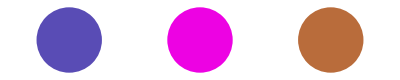

```mathematica
Graphics[{RGBColor[1-normRuifrok[[1]]],Disk[{0,0},0.25],RGBColor[1-normRuifrok[[2]]],Disk[{1,0},0.25],RGBColor[1-normRuifrok[[3]]],Disk[{2,0},0.25]}]
```

We can create a function that takes a grayscale image and a set of RGB weights as input and outputs a colorized version of the image where the grayscale has been converted to a monochromatic intensity scale related to the weighted RGB components. In Java, this would be an image with an indexed palette. I'm not sure how to do that in Mathematica, so the function will create a traditional, three-channel RGB image.

```mathematica
(*
Given a grayscale image and a set of RGB weights for the hue,produce a version of the image with the pixels colored with the intensity of the output hue being related to the darkness of the input gray pixels.
Input: 
img -- a grayscale image.
weights -- a list of the relative weights of the RGB channels for the desired hue.
Output: a new image colored with the desired hue.
*)
colorizeGrayImage[img_,weights_]:=Module[
{grayData,lut,rgbTuples,arr,newImg},
If[options[verbose]=="veryVerbose",{
Print["colorizeGrayImage: -----------------"];Print["weights: ",weights]}];
lut=Reverse[Table[{(255-(i*weights[[1]]))/255,(255-(i*weights[[2]]))/255,(255-(i*weights[[3]]))/255},{i,0,255}]];
If[options[verbose]=="veryVerbose",{Print["Dimensions[lut]: ", Dimensions[lut]];Print["lut: ", Take[lut,5],", ..."]}];
grayData=Flatten[ImageData[img,"Byte"]];
If[options[verbose]=="veryVerbose",{Print["Dimensions[grayData]: ", Dimensions[grayData]];Print["grayData: ",Take[grayData,5], ", ..."]}];
(* Create a new list of RGB values by mapping the grayscale data through the lookup table. *)
rgbTuples=lut[[#+1]]&/@grayData;
If[options[verbose]=="veryVerbose",{Print["Dimensions[rgbTuples]: ",Dimensions[rgbTuples]];
Print["rgbTuples: ", Take[rgbTuples, 5], ", ..."]}];
arr = Partition[rgbTuples, Part[Dimensions[ImageData[img]],2]];
If[options[verbose]=="veryVerbose",{Print["Max[arr]: ",Max[arr],", Min[arr]: ",Min[arr]];
Print["Dimensions[arr]: ", Dimensions[arr]];
Print["arr[[1]]: ", Take[arr[[1]],5], ", ..."]}];
newImg=Image[arr,ColorSpace->"RGB"];
If[options[verbose]=="veryVerbose",{Print["ImageQ[newImg]: ", ImageQ[newImg]];
Print["ImageType[newImg]: ",ImageType[newImg]];
Print["ImageChannels[newImg]: ",ImageChannels[newImg]]}];
newImg
]
```

```mathematica
(*
Create three colored images from an input list of grayscale images and a matrix of RGB weights. Each row of the weight matrix corresponds to the hue to be applied to the corresponding image.
*)
colorizeGrayImages[imgList_,weightMatrix_]:=
{colorizeGrayImage[imgList[[1]],weightMatrix[[1]]],
colorizeGrayImage[imgList[[2]],weightMatrix[[2]]],
colorizeGrayImage[imgList[[3]],weightMatrix[[3]]]}
```

```mathematica
colorizeGrayImages[csi,ruifrok]
```

{-Graphics-,-Graphics-,-Graphics-}

Of course, this is an image from an H&E stain -- there is no DAB in the stain. So the information for the third dye, which we contrived above, is bogus. What is needed is an intelligent way to deal with requests to deconvolute only two dyes. (Of course, there is no need to deconvolve a single dye.)

#### Dealing with Two or Three Stains

The ImageJ plugin for the method suggests a way to deal with the deconvolution when fewer than three dyes are provided in the color basis. The method used in the plugin is to fill in the third channel with the "complement" of the rest of the dyes.

First, the row normalization function can be made robust to "empty" weights.

```mathematica
normalizeBasisRobustly[basis_]:=Module[
{m,n},
m=Table[0,{i,3},{j,3}];
n=Norm[basis[[1]]];
m[[1]]=If[n≠0,basis[[1]]/n,basis[[1]]];
n=Norm[basis[[2]]];
m[[2]]=If[n≠0,basis[[2]]/n,basis[[2]]];
n=Norm[basis[[3]]];
m[[3]]=If[n≠0,basis[[3]]/n,basis[[3]]];
m
]
```

```mathematica
ruifrokHnE={{0.65,0.7,0.29},{0.07,0.99,0.11},{0,0,0}};
ruifrokHnE//MatrixForm
```

(0.65 | 0.7 | 0.29
0.07 | 0.99 | 0.11
0 | 0 | 0)

```mathematica
normHnE=normalizeBasisRobustly[ruifrokHnE];
normHnE//MatrixForm
```

(0.651108 | 0.701193 | 0.290494
0.0701017 | 0.991439 | 0.11016
0 | 0 | 0)

```mathematica
(*
A function to build a color deconvolution translation matrix given at least one set of weights for a dye. Missing dyes will be created that are complementary to the dyes present until information for three dyes has been created.
*)
buildTranslationMatrix[basis_]:=Module[
{m,nr},
(* First assure that we have a basis matrix of appropriate dimensionality, i.e. 3x3, and copy over the contents of the weights. *)
m=Table[{0,0,0},{i,1,3}];
nr=First[Dimensions[basis]];
m[[1;;nr]]=basis;
If[options[verbose]=="veryVerbose",{Print["Dimensions[basis]: ",Dimensions[basis]];
Print["nr: ",nr];
Print["m: ",m//MatrixForm];}];
m=normalizeBasisRobustly[m];
If[options[verbose]=="veryVerbose",Print["normalized m: ",m//MatrixForm]];
(* If second dye is unspecified, copy the first into it. *)
If[Norm[m[[2]]==0],m[[2]]=m[[1]]];
(* If third dye is unspecified fill with the complement of the others. *)
If[Norm[m[[3]]]==0,
{If[options[verbose]=="veryVerbose",Print["Filling third row"]];
If[m[[1,1]]*m[[1,1]]+m[[2,1]]*m[[2,1]]>1,{
If[options[verbose]=="veryVerbose",Print["Color 3 has negative R component"]];
m[[3,1]]=0;},
m[[3,1]]=Sqrt[1.0-m[[1,1]]*m[[1,1]]-m[[2,1]]*m[[2,1]]]];
If[m[[1,2]]*m[[1,2]]+m[[2,2]]*m[[2,2]]>1,{
If[options[verbose]=="veryVerbose",Print["Color 3 has negative G component"]];
m[[3,2]]=0;},
m[[3,2]]=Sqrt[1.0-m[[1,2]]*m[[1,2]]-m[[2,2]]*m[[2,2]]]];
If[m[[1,3]]*m[[1,3]]+m[[2,3]]*m[[2,3]]>1,{
If[options[verbose]=="veryVerbose",Print["Color 3 has negative G component"]];
m[[3,3]]=0;},
m[[3,3]]=Sqrt[1.0-m[[1,3]]*m[[1,3]]-m[[2,3]]*m[[2,3]]]];
(* Set any zero elements to a small positive number. *)
m=m/. 0->0.001;
If[options[verbose]=="veryVerbose",Print["m without zeros: ",m//MatrixForm]];
(* Normalize third dye color *)
m[[3]]=m[[3]]/Norm[m[[3]]];
}];
m
]
```

```mathematica
buildTranslationMatrix[{{0.644211,0.716556,0.266844},{0.092789,0.954111,0.283111}}]//MatrixForm
```

(0.644319 | 0.716676 | 0.266889
0.0928313 | 0.954546 | 0.28324
0.635954 | 0.000837772 | 0.771726)

### Putting It All Together

A single function to deconvolve an image, given and image and a basis matrix of color weights.

```mathematica
deconvolveByRuifrok[img_,basis_]:=Module[
{odPixels,translationMatrix,deconvAbs,deconvTrans,outArray},
odPixels=convertRgbTupleArrayToOD[convertToRgbTuples[img]];
translationMatrix=buildTranslationMatrix[basis];
deconvAbs=odPixels.Inverse[translationMatrix];
deconvTrans=convertOdTupleArrayToRgb[deconvAbs];
outArray=Partition[deconvTrans,Part[Dimensions[ImageData[img]],2]];
{Image[outArray,ColorSpace->"RGB"],translationMatrix}
]
```

```mathematica
{outImg,weights}=deconvolveByRuifrok[img,ruifrokHnE];
```

```mathematica
weights//MatrixForm
```

(0.651108 | 0.701193 | 0.290494
0.0701017 | 0.991439 | 0.11016
0.622347 | 0.000823492 | 0.782741)

```mathematica
outImg
```

-Graphics-

```mathematica
ColorSeparate[outImg]
```

{-Graphics-,-Graphics-,-Graphics-}

(Note the following usage. Do not pass in an RGB image, but a list of images.)

```mathematica
colorizeGrayImages[ColorSeparate[outImg],weights]
```

{-Graphics-,-Graphics-,-Graphics-}

Now let's try on a different, larger image.

```mathematica
bigImgPath = "~/projects/Color-Deconvolution/Images/61185 a.jpg";
bigImg = Import[bigImgPath]
```

-Graphics-

```mathematica
{outImg,weights}=deconvolveByRuifrok[bigImg,ruifrokHnE];
(*options[verbose]="veryVerbose";*)colorizeGrayImages[ColorSeparate[outImg],weights]
```

{-Graphics-,-Graphics-,-Graphics-}

That seems pretty good. Not too much "left over" in the unspecified channel.